# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Isotropic Scattering

```mathematica
pIsotropic[u_]:=1/(4Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pIsotropic[u],{u,-1,1}]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pIsotropic[u]u,{u,-1,1}]
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pIsotropic[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2 Pi (2k+1)pIsotropic[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

### sampling

```mathematica
cdf=Integrate[2 Pi pIsotropic[u],{u,-1,x}]
```

(1+x)/2

```mathematica
Solve[cdf==e,x]
```

{{x→-1+2 e}}

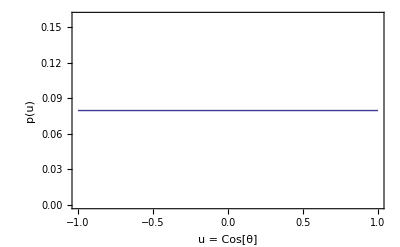

```mathematica
Clear[u];Show[
Plot[pIsotropic[u],{u,-1,1},PlotStyle->Thick]
,Frame->True,
FrameLabel->{{p[u],},{"u = Cos[θ]","Isotropic Scattering"}}]
```